### All possible single-cell diseases and treatments graph

#### Finding smaller cousing to main rule

```mathematica
Module[
{ru = {299459058088077826119326329530172894272,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},
Length[{{"[◼]", "allperts"}}[ru, init, txspec]]]
```

483

```mathematica
SeedRandom[111111+13];{{"[◼]", "RandomRuleMutation"}}[{299459058088077823758143088095350287424,4,1}]
```

{299459058088077826119326329530172894272,4,1}

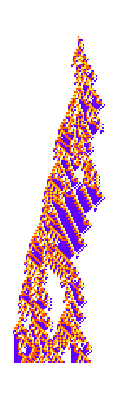
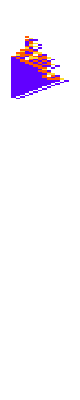
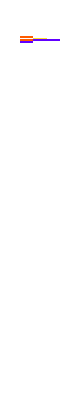
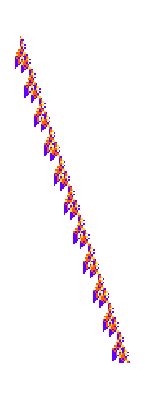
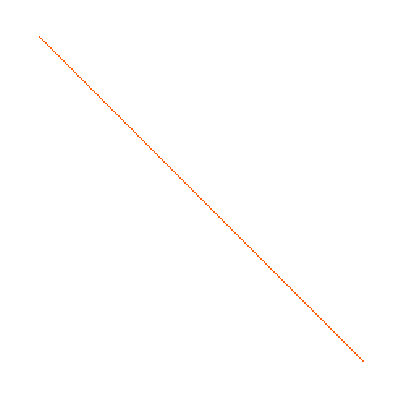
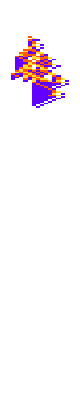
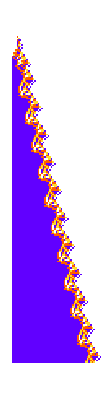
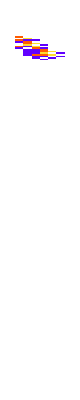
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[SeedRandom[111111+i];{{"[◼]", "PlotCA"}}[{{"[◼]", "RandomRuleMutation"}}[{299459058088077823758143088095350287424,4,1}]], {i, 30}]
```

```mathematica
Module[
{deep=100,cut=200,ru,life},
SeedRandom[5000+53];
{{"[◼]", "RulesMutationPlot"}}[
Take[First/@Split[First/@NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]
],{48,51}]]]
```

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

```mathematica
Row[With[{ru={299459058088077823758143088095350287424,4,1},pt=<|{15,206}->0|>},{{{"[◼]", "PlotCA"}}[ru,"Steps"->24,ImageSize->{Automatic,200},Mesh->All,MeshStyle->Opacity[.1]],{{"[◼]", "PlotCA"}}[ru,"Steps"->105,ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1]],Spacer[20],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{24,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,200}],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{105,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,450}]}],Spacer[10],Alignment->Bottom]
```

```mathematica
SeedRandom[111111+2];{{"[◼]", "RandomRuleMutation"}}[{299459058088077823758143088095350287424,4,1}]
```

{310092882054357150741373544577593044032,4,1}

```mathematica
Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {100,{-50, 50}}]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{299459058088077826119326329530172894272,4,1}, {{1}, 0}, {200,{-50, 50}}]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

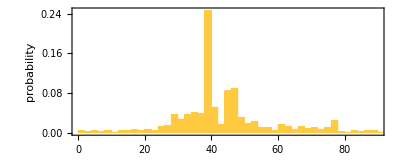

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},Histogram[lts = {{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ {{"[◼]", "allperts"}}[ru, init, txspec],  100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]]
```

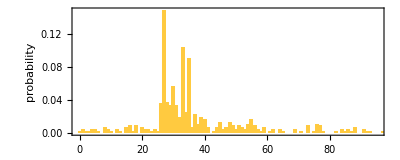

```mathematica
Module[
{ru = {299459058088077826119326329530172894272,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},Histogram[lts = {{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, #, "ReturnPerturbations"->False]]&/@ {{"[◼]", "allperts"}}[ru, init, txspec],  100, "Probability",Frame->True,AspectRatio->.4,FrameLabel->{"lifetime","probability"}]]
```

#### Getting all possible single-cell diseases and treatments

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},
aps = {{"[◼]", "allperts"}}[CellularAutomaton[ru, init, txspec], 4];
dis = Discard[aps, 35<={{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]<=50&];
Function[pert, {pert, #}&/@ Select[dis, Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]]/@ dis
]
```

```mathematica
ps = Function[pert, {pert, #}&/@ Select[dis, Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]]/@ dis;
```

```mathematica
pfs = Flatten[ps, 1];
```

```mathematica
ByteCount[ps]
```

39782520

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},plts = ParallelMap[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, Join@@#, "ReturnPerturbations"->False]]&, pfs]];
```

```mathematica
Iconize[plts]
```

```mathematica
plts = ;
```

```mathematica
ByteCount[plts]
```

1268912

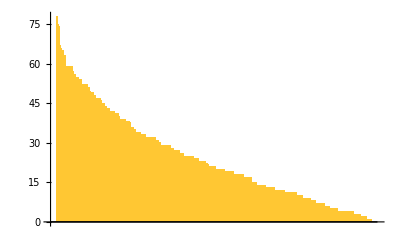

```mathematica
BarChart[Length/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length]]
```

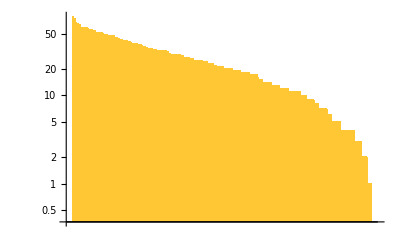

```mathematica
BarChart[Length/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length], ScalingFunctions->{"Log", "Log"}]
```

```mathematica
Length[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]
```

7884

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {50, {-110, 110}}, #]]&/@Join@@@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length][[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {50, {-110, 110}}, #[[1]]]]&/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length][[1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {50, {-110, 110}}, #[[1]]]]&/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {50, {-110, 110}}, Join@@#]]&/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {50, {-110, 110}}, #[[1]]]]&/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length][[3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{"[◼]", "PlotCA"}}[ResourceFunction["PerturbedCellularAutomaton"][{310092882054357150741373544577593044032,4,1}, {{1}, 0}, {50, {-110, 110}}, Join@@#]]&/@ReverseSortBy[GatherBy[pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]], #[[2]]&], Length][[3]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Pair graph

```mathematica
#1->#2&@@@pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]]
```

```mathematica
Graph[dis, #1->#2&@@@pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]]]
```

-Graphics-

```mathematica
LayeredGraph[#1->#2&@@@pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]]]
```

-Graphics-

```mathematica
VertexList[]
```

{<|{0,111}→0|>,<|{0,111}→2|>,<|{1,112}→0|>,<|{1,112}→2|>,<|{2,111}→0|>,<|{2,111}→2|>,<|{2,111}→3|>,<|{2,112}→0|>,<|{2,112}→1|>,<|{2,112}→3|>,<|{2,113}→1|>,<|{2,113}→3|>,<|{3,111}→1|>,<|{3,112}→0|>,<|{3,112}→2|>,<|{3,112}→3|>,<|{4,111}→0|>,<|{4,112}→0|>,<|{4,112}→2|>,<|{4,112}→3|>,<|{4,113}→1|>,<|{4,113}→2|>,<|{5,111}→0|>,<|{5,111}→1|>,<|{5,112}→0|>,<|{5,112}→2|>,<|{5,113}→1|>,<|{5,113}→2|>,<|{5,114}→1|>,<|{6,111}→0|>,<|{6,112}→0|>,<|{6,112}→2|>,<|{6,113}→0|>,<|{6,113}→1|>,<|{7,111}→0|>,<|{7,111}→1|>,<|{7,111}→2|>,<|{7,112}→1|>,<|{7,113}→1|>,<|{7,113}→3|>,<|{7,114}→0|>,<|{7,114}→1|>,<|{8,110}→2|>,<|{8,111}→0|>,<|{8,111}→2|>,<|{8,111}→3|>,<|{8,112}→3|>,<|{8,113}→0|>,<|{8,113}→1|>,<|{9,110}→0|>,<|{9,110}→2|>,<|{9,111}→0|>,<|{9,111}→1|>,<|{9,111}→3|>,<|{9,112}→0|>,<|{9,112}→2|>,<|{9,112}→3|>,<|{9,113}→0|>,<|{9,113}→2|>,<|{10,110}→0|>,<|{10,110}→2|>,<|{10,110}→3|>,<|{10,111}→0|>,<|{10,111}→1|>,<|{10,111}→3|>,<|{10,112}→0|>,<|{10,112}→1|>,<|{10,112}→3|>,<|{10,113}→0|>,<|{10,113}→2|>,<|{10,114}→0|>,<|{10,114}→1|>,<|{10,114}→2|>,<|{11,109}→0|>,<|{11,109}→1|>,<|{11,110}→0|>,<|{11,110}→2|>,<|{11,110}→3|>,<|{11,111}→0|>,<|{11,111}→3|>,<|{11,112}→2|>,<|{11,112}→3|>,<|{11,113}→1|>,<|{11,113}→2|>,<|{11,114}→0|>,<|{11,114}→2|>,<|{11,114}→3|>,<|{11,115}→0|>,<|{11,115}→1|>,<|{11,115}→3|>,<|{12,108}→0|>,<|{12,108}→2|>,<|{12,109}→1|>,<|{12,110}→0|>,<|{12,110}→2|>,<|{12,110}→3|>,<|{12,111}→0|>,<|{12,111}→1|>,<|{12,112}→0|>,<|{12,112}→1|>,<|{12,112}→2|>,<|{12,113}→0|>,<|{12,113}→3|>,<|{12,114}→0|>,<|{12,114}→1|>,<|{12,114}→3|>,<|{12,115}→3|>,<|{13,108}→1|>,<|{13,108}→3|>,<|{13,109}→0|>,<|{13,109}→2|>,<|{13,109}→3|>,<|{13,110}→0|>,<|{13,110}→3|>,<|{13,111}→1|>,<|{13,111}→2|>,<|{13,111}→3|>,<|{13,112}→1|>,<|{13,112}→2|>,<|{13,113}→1|>,<|{13,113}→2|>,<|{13,114}→3|>,<|{13,115}→0|>,<|{13,116}→0|>,<|{14,109}→0|>,<|{14,109}→1|>,<|{14,110}→0|>,<|{14,110}→2|>,<|{14,111}→1|>,<|{14,111}→2|>,<|{14,111}→3|>,<|{14,112}→2|>,<|{14,113}→0|>,<|{14,114}→0|>,<|{14,114}→2|>,<|{14,114}→3|>,<|{14,115}→1|>,<|{14,115}→3|>,<|{14,117}→1|>,<|{14,117}→3|>,<|{15,110}→0|>,<|{15,110}→2|>,<|{15,110}→3|>,<|{15,111}→0|>,<|{15,112}→0|>,<|{15,112}→1|>,<|{15,113}→0|>,<|{15,113}→2|>,<|{15,113}→3|>,<|{15,114}→0|>,<|{15,114}→1|>,<|{15,114}→3|>,<|{15,115}→0|>,<|{15,115}→2|>,<|{15,116}→3|>,<|{16,109}→3|>,<|{16,111}→0|>,<|{16,111}→2|>,<|{16,111}→3|>,<|{16,112}→0|>,<|{16,113}→0|>,<|{16,113}→1|>,<|{16,113}→3|>,<|{16,114}→0|>,<|{16,114}→2|>,<|{16,114}→3|>,<|{16,115}→0|>,<|{16,115}→1|>,<|{16,115}→3|>,<|{16,116}→0|>,<|{16,116}→2|>,<|{16,116}→3|>,<|{17,108}→1|>,<|{17,108}→3|>,<|{17,110}→3|>,<|{17,111}→0|>,<|{17,111}→3|>,<|{17,112}→0|>,<|{17,112}→2|>,<|{17,112}→3|>,<|{17,113}→0|>,<|{17,113}→3|>,<|{17,114}→0|>,<|{17,114}→1|>,<|{17,115}→0|>,<|{17,115}→2|>,<|{17,116}→0|>,<|{17,116}→2|>,<|{17,117}→1|>,<|{18,108}→1|>,<|{18,109}→1|>,<|{18,110}→3|>,<|{18,112}→0|>,<|{18,112}→3|>,<|{18,113}→0|>,<|{18,113}→2|>,<|{18,113}→3|>,<|{18,114}→0|>,<|{18,114}→3|>,<|{18,115}→3|>,<|{18,116}→3|>,<|{18,117}→1|>,<|{18,117}→3|>,<|{18,118}→3|>,<|{19,109}→1|>,<|{19,109}→3|>,<|{19,110}→1|>,<|{19,110}→3|>,<|{19,111}→3|>,<|{19,112}→3|>,<|{19,113}→0|>,<|{19,113}→3|>,<|{19,114}→0|>,<|{19,114}→2|>,<|{19,114}→3|>,<|{19,115}→0|>,<|{19,116}→3|>,<|{19,117}→1|>,<|{19,117}→3|>,<|{20,108}→3|>,<|{20,110}→1|>,<|{20,110}→3|>,<|{20,111}→1|>,<|{20,113}→3|>,<|{20,114}→0|>,<|{20,114}→1|>,<|{20,114}→3|>,<|{20,115}→0|>,<|{20,115}→1|>,<|{20,115}→2|>,<|{21,108}→3|>,<|{21,110}→3|>,<|{21,111}→1|>,<|{21,112}→1|>,<|{21,113}→0|>,<|{21,113}→3|>,<|{21,114}→3|>,<|{21,115}→0|>,<|{21,115}→3|>,<|{21,116}→3|>,<|{22,108}→3|>,<|{22,109}→3|>,<|{22,110}→3|>,<|{22,112}→1|>,<|{22,113}→1|>,<|{22,114}→0|>,<|{22,115}→0|>,<|{22,115}→3|>,<|{22,116}→3|>,<|{23,108}→3|>,<|{23,110}→3|>,<|{23,111}→3|>,<|{23,113}→1|>,<|{23,113}→3|>,<|{23,114}→1|>,<|{23,114}→3|>,<|{23,115}→0|>,<|{23,115}→1|>,<|{23,115}→3|>,<|{23,116}→0|>,<|{23,117}→1|>,<|{24,108}→3|>,<|{24,110}→3|>,<|{24,114}→1|>,<|{24,114}→3|>,<|{24,115}→0|>,<|{24,116}→3|>,<|{24,117}→3|>,<|{24,118}→0|>,<|{24,118}→1|>,<|{25,108}→3|>,<|{25,109}→3|>,<|{25,112}→3|>,<|{25,114}→3|>,<|{25,115}→3|>,<|{25,116}→0|>,<|{25,117}→0|>,<|{25,117}→3|>,<|{26,108}→3|>,<|{26,110}→3|>,<|{26,111}→3|>,<|{26,114}→3|>,<|{26,116}→0|>,<|{26,116}→3|>,<|{26,117}→3|>,<|{26,118}→0|>,<|{27,110}→3|>,<|{27,117}→3|>,<|{27,119}→3|>,<|{28,108}→3|>,<|{28,109}→3|>,<|{28,110}→3|>,<|{28,116}→3|>,<|{28,118}→3|>,<|{29,108}→3|>,<|{29,110}→3|>,<|{29,115}→3|>,<|{29,117}→3|>,<|{30,108}→3|>,<|{30,110}→3|>,<|{30,114}→3|>,<|{30,116}→3|>,<|{31,108}→3|>,<|{31,109}→3|>,<|{31,110}→3|>,<|{31,113}→3|>,<|{31,115}→3|>,<|{32,108}→3|>,<|{32,109}→3|>,<|{32,110}→3|>,<|{32,112}→3|>,<|{32,114}→3|>,<|{33,108}→3|>,<|{33,109}→3|>,<|{33,110}→3|>,<|{33,111}→3|>,<|{33,113}→3|>,<|{34,108}→3|>,<|{34,110}→3|>,<|{34,112}→3|>,<|{35,108}→1|>,<|{35,108}→3|>,<|{35,109}→3|>,<|{35,111}→3|>,<|{36,108}→3|>,<|{36,109}→1|>,<|{36,109}→3|>,<|{36,110}→3|>,<|{37,109}→3|>,<|{38,109}→1|>,<|{38,109}→3|>}

```mathematica
VertexDegree[]
```

{42,42,42,42,37,35,81,37,79,55,34,26,89,38,34,86,23,34,20,30,21,20,25,26,35,30,34,23,55,30,33,22,101,68,30,42,24,38,38,74,49,47,20,18,9,64,65,50,77,28,20,42,51,84,42,56,71,64,33,25,20,86,65,81,73,57,86,80,94,61,42,56,47,55,89,46,106,104,39,78,33,74,83,42,44,29,44,54,55,54,30,35,77,51,53,61,55,51,45,52,47,34,92,52,71,55,72,59,47,26,30,75,61,86,50,39,69,51,44,61,46,73,59,55,43,79,27,33,55,50,64,74,53,55,50,62,58,70,81,73,50,55,95,64,50,45,65,59,65,62,51,57,48,49,81,63,46,43,62,59,46,53,57,59,49,78,32,55,43,47,53,90,75,50,93,57,85,48,53,44,59,73,65,50,67,55,49,94,56,53,78,66,51,61,47,56,76,53,63,61,59,94,65,82,57,47,76,60,81,71,48,60,34,60,47,47,68,37,40,36,58,58,84,63,39,67,66,46,80,35,52,31,57,88,36,70,57,52,63,97,54,62,52,63,84,24,44,63,62,13,48,63,57,54,65,59,52,44,38,47,31,41,32,69,50,23,57,25,22,29,17,48,73,49,66,14,13,39,25,33,69,50,12,39,24,20,33,20,22,13,23,27,25,14,17,41,25,16,7,15,9,14,21,8,7,14,14,9,7,10,19,8,2,9,12,12,11,3,5,3,20,2,10,3,3,5,5,5,1,2,4}

#### Pair matrix

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=50&]]]]]
```

-Graphics-

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 35<=plts[[#]]<=45&]]]]]
```

-Graphics-

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 37.5<=plts[[#]]<=42.5&]]]]]
```

-Graphics-

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 20<=plts[[#]]<=60&]]]]]
```

-Graphics-

#### Gradient matrix

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},
aps = {{"[◼]", "allperts"}}[CellularAutomaton[ru, init, txspec], 4];
dis = Discard[aps, 35<={{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #]]<=50&];
Function[pert, {pert, #}&/@ Select[dis, Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]]/@ dis
]
```

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},{{"[◼]", "TestCALifeTime"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, <||>]]]
```

39

```mathematica
Length[dis]
```

331

```mathematica
Split[]
```

```mathematica
Partition[plts, Length/@GatherBy[pfs, First]]
```

```mathematica
Length/@GatherBy[pfs, First]
```

{329,329,327,327,319,319,319,319,319,319,319,319,315,315,315,315,309,309,309,309,309,309,302,302,302,302,302,302,302,297,297,297,297,297,289,289,289,289,289,289,289,289,282,282,282,282,282,282,282,272,272,272,272,272,272,272,272,272,272,258,258,258,258,258,258,258,258,258,258,258,258,258,258,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,241,224,224,224,224,224,224,224,224,224,224,224,224,224,224,224,224,224,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,207,191,191,191,191,191,191,191,191,191,191,191,191,191,191,191,191,176,176,176,176,176,176,176,176,176,176,176,176,176,176,176,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,142,127,127,127,127,127,127,127,127,127,127,127,127,127,127,127,112,112,112,112,112,112,112,112,112,112,112,112,112,112,112,101,101,101,101,101,101,101,101,101,101,101,91,91,91,91,91,91,91,91,91,91,82,82,82,82,82,82,82,82,82,70,70,70,70,70,70,70,70,70,70,70,70,61,61,61,61,61,61,61,61,61,53,53,53,53,53,53,53,53,45,45,45,45,45,45,45,45,42,42,42,37,37,37,37,37,33,33,33,33,29,29,29,29,24,24,24,24,24,19,19,19,19,19,14,14,14,14,14,11,11,11,7,7,7,7,3,3,3,3,2}

```mathematica
Length[dis]
```

331

```mathematica
sa = MapIndexed[Join[First[Position[dis, #[[1]]]],First[Position[dis, #[[2]]]]] ->Abs[plts[[#2[[1]]]] - 39]&, pfs];
```

```mathematica
sa
```

```mathematica
arr = ReplacePart[Table[-1, {i, Length[dis]}, {j, Length[dis]}], sa];
```

```mathematica
arr[[100]]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,5,3,10,9,72,11,65,11,9,21,9,11,11,11,16,14,11,12,11,10,9,6,11,44,9,7,11,11,8,8,7,11,13,12,11,3,10,11,6,9,9,16,15,9,11,11,11,3,7,12,11,46,10,11,6,11,9,9,13,13,16,3,11,11,3,4,6,1,12,2,12,11,28,10,6,14,6,9,9,11,9,16,6,4,11,12,4,15,11,9,10,13,38,11,41,0,4,6,5,4,124,1,4,12,10,12,11,16,13,3,11,12,13,6,54,4,16,13,6,9,11,4,10,90,15,6,4,13,9,3,12,12,1,15,8,19,6,4,12,11,1,11,18,6,9,11,12,5,1,11,10,11,11,23,13,9,10,11,11,23,23,11,24,18,20,1,24,24,11,11,24,2,10,1,25,11,25,25,11,19,26,26,27,27,27,27,27,28,28,28,28,29,29,29,29,30,30,30,30,30,31,31,31,31,31,32,32,32,32,32,33,33,33,35,34,34,34,35,36,35,35,36,38,37}

```mathematica
Table[Blend[{Darker[Blue],  LightBlue, White},i], {i, 0, 1, .1}]
```

{RGBColor[0., 0., 0.6666666666666666],RGBColor[0.17400000000000002, 0.188, 0.7333333333333333],RGBColor[0.34800000000000003, 0.376, 0.8],RGBColor[0.522, 0.5640000000000001, 0.8666666666666667],RGBColor[0.6960000000000001, 0.752, 0.9333333333333333],RGBColor[0.87, 0.94, 1.],RGBColor[0.896, 0.952, 1.],RGBColor[0.922, 0.964, 1.],RGBColor[0.948, 0.976, 1.],RGBColor[0.974, 0.988, 1.],RGBColor[1., 1., 1.]}

```mathematica
arr[[;;10, ;;10]]
```

{{-1,-1,39,37,39,36,1,39,2,1},{-1,-1,38,37,38,36,1,38,2,1},{-1,-1,-1,-1,38,36,1,38,2,1},{-1,-1,-1,-1,37,36,1,37,2,1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}}

```mathematica
ArrayPlot[arr, ColorRules->{-1->White},ColorFunction->(If[# == -1, White,Blend[{Lighter[Blue],  LightBlue, White},#]]&)]
```

-Graphics-

```mathematica
ArrayPlot[arr, ColorRules->{-1->White},ColorFunction->(If[# == -1, White,Blend[{Purple, Blue, LightBlue, White},#]]&)]
```

-Graphics-

```mathematica
ArrayPlot[arr, ColorRules->{-1->White},ColorFunction->(If[# == -1, White,Blend[{Darker[Blue], Purple, Lighter[Purple], White},#]]&)]
```

-Graphics-

```mathematica
ArrayPlot[arr, ColorRules->{-1->White},ColorFunction->(If[# == -1, White,Blend[{LightGray,  Lighter[Red], Red},#]]&)]
```

-Graphics-

```mathematica
SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 20<=plts[[#]]<=60&]]]]
```

```mathematica
ArrayPlot[SparseArray[Join[First[Position[dis, #1]],First[Position[dis, #2]]] ->1&@@@pfs[[Select[Range[Length[pfs]], 20<=plts[[#]]<=60&]]]], ColorFunction->(Blend[{White,LightBlue,Blue},#]&)]
```

```mathematica
Module[{rule={240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664,6,1},ca,capert,pert=<|{3,7}->4|>,colrules=Join[{0->White,1->Darker[Blue]},Table[i->Blend[{White,LightBlue,Blue},i/5],{i,2,5}]]},caperts=Table[[rule,{Join[Table[1,j],{2}],0},{80,{-5,15}},#],{j,1,5}]&/@{<||>,pert};
GraphicsRow[Function[{ca,pert},{{"[◼]", "PerturbedArrayPlot"}}[ca,If[pert==<||>,{},First[Keys[pert]]],ColorRules->colrules,Mesh->True,MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9],Haloing[Red]],"ArrowDirection"->Left,ImageSize->{Automatic,300}]]@@@#]&@caperts[[1]]]
```

#### Correcting single-cell disease and treatment algo

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},
aps = {{"[◼]", "allperts"}}[CellularAutomaton[ru, init, txspec], 4]];
```

```mathematica
aps[[1]]
```

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}},
aaps = ParallelMap[{{"[◼]", "allperts"}}[ResourceFunction["PerturbedCellularAutomaton"][ru, init, txspec, #], 4]&, aps]];
```

SparseArray::list: List expected at position 1 in SparseArray[<|{0,111}→0|>].

SparseArray::list: List expected at position 1 in SparseArray[<|{7,111}→1|>].

Part::partd: Part specification SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[<|{7,111}→1|>][NonzeroPositions]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦-1,1⟧ is longer than depth of object.

Part::partd: Part specification SparseArray[<|{7,111}→1|>][NonzeroPositions]⟦-1,1⟧ is longer than depth of object.

Range::range: Range specification in Range[SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦1,1⟧,SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦-1,1⟧] does not have appropriate bounds.

Range::range: Range specification in Range[SparseArray[<|{7,111}→1|>][NonzeroPositions]⟦1,1⟧,SparseArray[<|{7,111}→1|>][NonzeroPositions]⟦-1,1⟧] does not have appropriate bounds.

Range::range: Range specification in Range[SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦1,1⟧,SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦-1,1⟧] does not have appropriate bounds.

Range::range: Range specification in Range[SparseArray[<|{7,111}→1|>][NonzeroPositions]⟦1,1⟧,SparseArray[<|{7,111}→1|>][NonzeroPositions]⟦-1,1⟧] does not have appropriate bounds.

Function::fpct: Too many parameters in {FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$} to be filled from Function[{FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$},(Association[{FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`i$-1,FunctionRepository`$ef0a888bb6b74e40bdae2147b79a0241`j$}→#1]&)/@Delete[Range[0,4-1],{{{«221»},«49»,«351»},<|«1»|>}⟦«1»⟧+1]][1].

Delete::partw: Part 1 of 0 does not exist.

Part::pkspec1: The expression SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦1,1⟧ cannot be used as a part specification.

Delete::pkspec: The expression <|{0,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«67»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|> cannot be used as a part specification. Use Key[<|{0,1}→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«67»,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}|>] instead.

Part::pkspec1: The expression SparseArray[<|{0,111}→0|>][NonzeroPositions]⟦1,1⟧ cannot be used as a part specification.

Delete::partw: Part 1 of 0 does not exist.

```mathematica
ps = Function[pert, {pert, #}&/@ Select[dis, Keys[#][[1, 1]]> Keys[pert][[1, 1]]&]]/@ dis;
```

```mathematica
pfs = Flatten[ps, 1];
```

```mathematica
ByteCount[ps]
```

39782520

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},plts = ParallelMap[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, Join@@#, "ReturnPerturbations"->False]]&, pfs]];
```

#### Scratchpad

```mathematica
Module[
{ru = {310092882054357150741373544577593044032,4,1},init = {{1}, 0}, txspec = {400, {-110, 110}}, aps},aaps = ParallelMap[{{"[◼]", "TestCALifeTime"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, init, txspec, Join@@#, "ReturnPerturbations"->False]]&, pfs]
```

```mathematica
Join@@pfs[[1]]
```

<|{0,111}→0,{1,112}→0|>

```mathematica
Length[ps]
```

331

```mathematica
Length[Catenate[ps]]
```

52868

```mathematica
Length[dis]
```

331

### By hand

### Machine learning

### Adaptive “search for drugs”